```mathematica
Fs=20000;
```

```mathematica
b=6
```

6

Continuous representation of a snap.

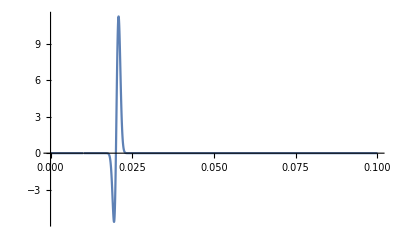

```mathematica
snap[t_]=ⅇ^((t-0.01)/0.002)ⅇ^(-((t-0.02)/0.001)^2)Sin[2π 100t]UnitStep[t-0.01]/5;
Plot[snap[t],{t,0,0.1},PlotRange->All]
```

The signal the ADC sees (as an integer and with noise), but seconds as time.

```mathematica
Signal[f_,t_,τ_]:=Round[2^b f[t-τ]+5*Sin[RandomReal[]]RandomVariate[NormalDistribution[0,2^4]]];
```

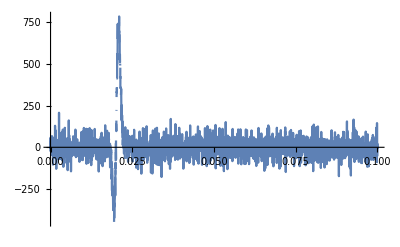

```mathematica
Plot[Signal[snap,t,0],{t,0,0.1},PlotRange->All]
```

Sampled with sample rate Fs, for Ts seconds.

```mathematica
N[0.01]
```

0.01

```mathematica
SampledSignal[f_,τ_,Ns_]:=Table[Signal[f,t,τ],{t,0,(Ns-1)/Fs,1/Fs}]
```

```mathematica
SampledSignal[snap,0.01,10]
```

{-8,2,-1,4,16,-6,2,4,12,-3}

s1 and s2 are “simulated” buffer contents.

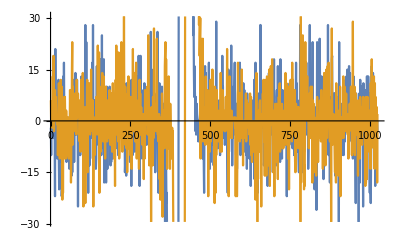

```mathematica
bufferSize = 1024;
s1=SampledSignal[snap,0,bufferSize];
s2 =SampledSignal[snap,0.001,bufferSize];
ListLinePlot[{s1,s2}]
```

```mathematica
pad[sampled_,n_]:=If[0<n<=bufferSize,sampled[[n]],0];
```

```mathematica
(*crossed[n_]:=∑_(k=-bufferSize)^bufferSize pad[s2,-n+k]pad[s1,k]*)
```

```mathematica
crossed[n_]:=∑_(k=-bufferSize)^bufferSize s1[[Mod[n+k,bufferSize]+1]]s2[[Mod[k,bufferSize]+1]]
```

```mathematica
crossed[300]
```

-85540

```mathematica
MaximalBy[Table[{crossed[n],n},{n,-bufferSize/2,bufferSize/2}],First]
```

{{22491872,-20}}

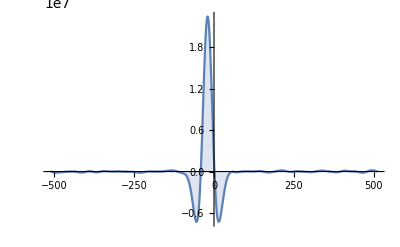

```mathematica
DiscretePlot[crossed[n],{n,-bufferSize/2,bufferSize/2},PlotRange->All]
```